```mathematica
cana20150817=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\cana20150817.xlsx"];
```

```mathematica
tempo=Table[cana20150817[[1,i,1]],{i,1,Length[cana20150817[[1]]]}];
```

```mathematica
transp=Table[cana20150817[[1,i,2]],{i,1,Length[cana20150817[[1]]]}];
```

```mathematica
par=Table[cana20150817[[1,i,3]],{i,1,Length[cana20150817[[1]]]}];
```

```mathematica
dpv=Table[cana20150817[[1,i,4]],{i,1,Length[cana20150817[[1]]]}];
```

```mathematica
transpVsTempo=ToExpression[Flatten/@Map[StringSplit[#,","]&,N[Table[{tempo[[i]],transp[[i]]},{i,1,Length[tempo]}]]]];
```

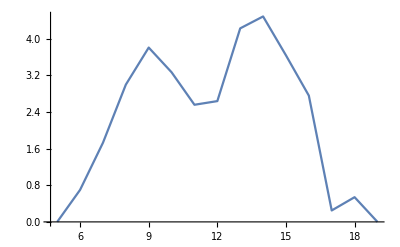

```mathematica
ListLinePlot[transpVsTempo]
```